# Two-port simulator

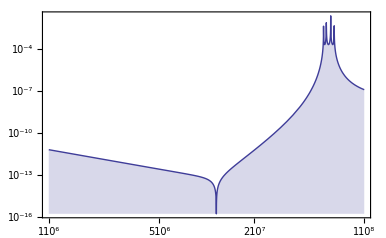

### Author

Jan G. Korvink © 2013, ..., 2021

### Concept

This package facilitates the simulation of two-port networks. The design philosophy is as follows:

Specify: a circuit is specified using custom Mathematica heads. There are heads for primitive circuit elements such as resistors, inductances and capacitances, and combinations of elements in series or parallel, all of which are called objects. The primitive circuit elements are used to specify two-ports. Further specifications allow the interconnection of two-ports into circuits.


Verify: a circuit is checked for correctness by plotting it with the function CircuitGraphics[], which can handle two-ports as well as interconnections of two-ports.

Compute: a circuit can be converted into an expression using the function CircuitExpression[]. Different representations are possible.

Manipulate: conversions are possible between various representations of the two-ports. Also, methodology is provided to generate two-ports from nodal analysis models.

Analyse: a circuit can be simulated.

Complement: for example, the impedance matching network of a circuit can be computed.

Embed: a circuit can be embedded in another representation.

### Usage

This gets the package:
fileName=StringJoin[NotebookDirectory[],”TwoPort.m”];
Get[fileName]

This lists the functions:
Names[“Twoport`*”]

### Todo features list:

+ How to make a balanced ABCD system? How to place items in the lower axis, so to speak?
+ Sources
+ Noise models
+ Stripline, and Cable twoport
+ Arbitrary networks
+ Circuit operators
+ Tidy up amplitude and phase
+ Netlist generation
+ Fixed size text in graphics (Scaled[] refers to the the entire plot range! Font size to the screen.
+ Plots: Nyquist (Transfer function, Im[] vs Re[], ω as parameter), Bode (dB of Power vs ω), Smith (Impedance Im[] vs Re[]), Root locus or Evans, Nichols or Black (|G(s)| vs Arg[G(s)]

Done:
+ Import 2 port models
+ Transistors
+ Smart evaluation and plotting of S-parameters.
+ Coupled inductor twoport (NO PLOT!)
+ Waveguide. 
+ Many conversions are missing.
+ Are the S-parameter conversions correctly implemented?

### References

1. Charles A. Desoer and Ernest S. Kuh, Basic Circuit Theory, McGraw-Hill, 1966
2. Wilfried Weißgerber, Elektrotechnik für Ingenieure 3, Vieweg 2007
3. K. C. Gupta, Peter S. Hall (Editors), Analysis and Design of Integrated Circuit Antenna Modules, Wiley Interscience, 1999
4. http://en.wikipedia.org/wiki/Electronic_filter_topology

### The functions and their use

```mathematica
fileName=StringJoin[NotebookDirectory[],"TwoPort.m"];
Get[fileName]
```

## The systematic package test examples

### Names of items

```mathematica
Names["Twoport`Oneport*"]
Names["Twoport`Impedance*"]
Names["Twoport`Twoport*"]
Names["Twoport`To*"]
Names["Twoport`Circuit*"]
Complement[Names["Twoport`*"],Names["Twoport`Oneport*"],Names["Twoport`Impedance*"],
Names["Twoport`Twoport*"],Names["Twoport`To*"],
Names["Twoport`Circuit*"]
]
```

{OneportC,OneportCImpedance,OneportConversionRules,OneportCS,OneportL,OneportLImpedance,OneportOpenStub,OneportOpenStubImpedance,OneportParallel,OneportParallelImpedance,OneportR,OneportRImpedance,OneportSeries,OneportSeriesImpedance,OneportShortedStub,OneportShortedStubImpedance,OneportTerminatedStub,OneportTerminatedStubImpedance,OneportVS,OneportZ,OneportZImpedance}

{}

{Twoport,TwoportBalancedLadder,TwoportBalancedLadderABCD,TwoportBoxsection,TwoportBoxsectionABCD,TwoportBridge,TwoportBridgeABCD,TwoportConversionRules,TwoportCoupledInductors,TwoportCoupledInductorsABCD,TwoportCsection,TwoportCsectionABCD,TwoportGammaI,TwoportGammaIABCD,TwoportGammaII,TwoportGammaIIABCD,TwoportGyrator,TwoportGyratorABCD,TwoportHsection,TwoportHsectionABCD,TwoportInvert,TwoportInvertABCD,TwoportLeftRight,TwoportLeftRightABCD,TwoportLossyWaveguide,TwoportLossyWaveguideABCD,TwoportMeasure,TwoportNMOScd,TwoportNMOScdABCD,TwoportNMOScg,TwoportNMOScgABCD,TwoportNMOScs,TwoportNMOScsABCD,TwoportNPNcb,TwoportNPNcbABCD,TwoportNPNcc,TwoportNPNccABCD,TwoportNPNce,TwoportNPNceABCD,TwoportPi,TwoportPiABCD,TwoportSeries,TwoportSeriesABCD,TwoportSeriesDown,TwoportSeriesDownABCD,TwoportShunt,TwoportShuntABCD,TwoportSwapTopBottom,TwoportTee,TwoportTeeABCD,TwoportTransformer,TwoportTransformerABCD,TwoportUnbalancedLadder,TwoportUnbalancedLadderABCD,TwoportWaveguide,TwoportWaveguideABCD,TwoportXsection,TwoportXsectionABCD,TwoportXsectionPi,TwoportXsectionPiABCD,TwoportXsectionTee,TwoportXsectionTeeABCD}

{ToA,ToB,ToH,ToP,ToS,ToT,Touchstone,ToY,ToZ}

{CircuitCascade,CircuitExpression,CircuitGraphics,CircuitHybrid,CircuitInverseHybrid,CircuitParallel,CircuitSerial}

{AllOneports,AllOneportsPattern,AllTwoportMatrices,AllTwoportMatricesPattern,AllTwoports,AllTwoportsPattern,Amplitude,Comment,CompleteTwoportMatrices,CompleteTwoportMatricesPattern,DrawCompound,DrawTwoport,ExtractTouchstoneNetwork,GridArrangement,JoinConversionRules,LogLinearPlotSparameters,matrixA,matrixB,MatrixFormat,matrixH,matrixP,matrixS,matrixT,matrixY,matrixZ,MixedModeOrder,NetworkData,NodalAdmittanceAssemble,NodalToTwoport,NodalY,NoiseData,NumberOfFrequencies,NumberOfNoiseFrequencies,NumberOfPorts,Optionline,Phase,plotFunction,PlotSparameters,PowerSolveABCD,ReadTouchstone,Reference,SmithPlot,SolveABCD,SolveIntermediateABCD,TwoPortDataOrder,UnwrapPhase,WriteTouchstone}

### Circuit specification and graphics

#### Circuit specification

```mathematica
testCircuitItems=
{TwoportShunt[OneportR[1]],
TwoportShunt[OneportL[1]],
TwoportShunt[OneportC[1]],
TwoportShunt[OneportShortedStub[1,1,1]],
TwoportShunt[OneportOpenStub[1,1,1]],

TwoportSeries[OneportR[1]],
TwoportSeries[OneportL[1]],
TwoportSeries[OneportC[1]],
TwoportSeries[OneportShortedStub[1,1,1]],
TwoportSeries[OneportOpenStub[1,1,1]],

TwoportSeriesDown[OneportR[1]],
TwoportSeriesDown[OneportL[1]],
TwoportSeriesDown[OneportC[1]],
TwoportSeriesDown[OneportShortedStub[1,1,1]],
TwoportSeriesDown[OneportOpenStub[1,1,1]],

TwoportLeftRight[OneportR[1],OneportL[1]],
TwoportLeftRight[OneportL[1],OneportR[1]],
TwoportLeftRight[OneportOpenStub[1],OneportShortedStub[1]],
TwoportLeftRight[OneportShortedStub[1],OneportOpenStub[1]],
TwoportLeftRight[OneportC[1],OneportC[1]],

TwoportGyrator[1],
TwoportGyrator[-1],
TwoportWaveguide[1,2,3],
TwoportTransformer[1],
TwoportInvert[],

TwoportPi[OneportR[1],OneportR[1],OneportR[1]],
TwoportPi[OneportL[1],OneportL[1],OneportL[1]],
TwoportPi[OneportC[1],OneportC[1],OneportC[1]],
TwoportPi[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],
TwoportPi[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],

TwoportTee[OneportR[1],OneportR[1],OneportR[1]],
TwoportTee[OneportL[1],OneportL[1],OneportL[1]],
TwoportTee[OneportC[1],OneportC[1],OneportC[1]],
TwoportTee[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],
TwoportTee[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],

TwoportGammaI[OneportR[1],OneportR[1]],
TwoportGammaI[OneportL[1],OneportL[1]],
TwoportGammaI[OneportC[1],OneportC[1]],
TwoportGammaI[OneportOpenStub[1],OneportOpenStub[1]],
TwoportGammaI[OneportShortedStub[1],OneportShortedStub[1]],

TwoportGammaII[OneportR[1],OneportR[1]],
TwoportGammaII[OneportL[1],OneportL[1]],
TwoportGammaII[OneportC[1],OneportC[1]],
TwoportGammaII[OneportOpenStub[1],OneportOpenStub[1]],
TwoportGammaII[OneportShortedStub[1],OneportShortedStub[1]],

TwoportCsection[OneportR[1],OneportR[1]],
TwoportCsection[OneportL[1],OneportL[1]],
TwoportCsection[OneportC[1],OneportC[1]],
TwoportCsection[OneportOpenStub[1],OneportOpenStub[1]],
TwoportCsection[OneportShortedStub[1],OneportShortedStub[1]],

TwoportHsection[OneportR[1],OneportR[1]],
TwoportHsection[OneportL[1],OneportL[1]],
TwoportHsection[OneportC[1],OneportC[1]],
TwoportHsection[OneportOpenStub[1],OneportOpenStub[1]],
TwoportHsection[OneportShortedStub[1],OneportShortedStub[1]],

TwoportBoxsection[OneportR[1],OneportR[1]],
TwoportBoxsection[OneportL[1],OneportL[1]],
TwoportBoxsection[OneportC[1],OneportC[1]],
TwoportBoxsection[OneportOpenStub[1],OneportOpenStub[1]],
TwoportBoxsection[OneportShortedStub[1],OneportShortedStub[1]],

TwoportXsection[OneportR[1],OneportR[1]],
TwoportXsection[OneportL[1],OneportL[1]],
TwoportXsection[OneportC[1],OneportC[1]],
TwoportXsection[OneportOpenStub[1],OneportOpenStub[1]],
TwoportXsection[OneportShortedStub[1],OneportShortedStub[1]],

TwoportBridge[OneportR[1],OneportR[1],OneportR[1],OneportR[1]],
TwoportBridge[OneportL[1],OneportL[1],OneportL[1],OneportL[1]],
TwoportBridge[OneportC[1],OneportC[1],OneportC[1],OneportC[1]],
TwoportBridge[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],
TwoportBridge[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],

TwoportUnbalancedLadder[OneportR[1]],
TwoportUnbalancedLadder[OneportL[1]],
TwoportUnbalancedLadder[OneportC[1]],
TwoportUnbalancedLadder[OneportShortedStub[1,1,1]],
TwoportUnbalancedLadder[OneportOpenStub[1,1,1]],

TwoportBalancedLadder[OneportR[1]],
TwoportBalancedLadder[OneportL[1]],
TwoportBalancedLadder[OneportC[1]],
TwoportBalancedLadder[OneportShortedStub[1,1,1]],
TwoportBalancedLadder[OneportOpenStub[1,1,1]],

TwoportXsectionTee[OneportR[1]],
TwoportXsectionTee[OneportL[1]],
TwoportXsectionTee[OneportC[1]],
TwoportXsectionTee[OneportShortedStub[1,1,1]],
TwoportXsectionTee[OneportOpenStub[1,1,1]],

TwoportXsectionPi[OneportR[1]],
TwoportXsectionPi[OneportL[1]],
TwoportXsectionPi[OneportC[1]],
TwoportXsectionPi[OneportShortedStub[1,1,1]],
TwoportXsectionPi[OneportOpenStub[1,1,1]],

TwoportNPNce[1,1,1],
TwoportNPNcb[1,1,1],
TwoportNPNcc[1,1,1],
TwoportInvert[],
TwoportInvert[],

TwoportNMOScs[1,1,1],
TwoportNMOScg[1,1,1],
TwoportNMOScd[1,1,1],
TwoportInvert[],
TwoportInvert[]

}
```

{TwoportShunt[OneportR[1]],TwoportShunt[OneportL[1]],TwoportShunt[OneportC[1]],TwoportShunt[OneportShortedStub[1,1,1]],TwoportShunt[OneportOpenStub[1,1,1]],TwoportSeries[OneportR[1]],TwoportSeries[OneportL[1]],TwoportSeries[OneportC[1]],TwoportSeries[OneportShortedStub[1,1,1]],TwoportSeries[OneportOpenStub[1,1,1]],TwoportSeriesDown[OneportR[1]],TwoportSeriesDown[OneportL[1]],TwoportSeriesDown[OneportC[1]],TwoportSeriesDown[OneportShortedStub[1,1,1]],TwoportSeriesDown[OneportOpenStub[1,1,1]],TwoportLeftRight[OneportR[1],OneportL[1]],TwoportLeftRight[OneportL[1],OneportR[1]],TwoportLeftRight[OneportOpenStub[1],OneportShortedStub[1]],TwoportLeftRight[OneportShortedStub[1],OneportOpenStub[1]],TwoportLeftRight[OneportC[1],OneportC[1]],TwoportGyrator[1],TwoportGyrator[-1],TwoportWaveguide[1,2,3],TwoportTransformer[1],TwoportInvert[],TwoportPi[OneportR[1],OneportR[1],OneportR[1]],TwoportPi[OneportL[1],OneportL[1],OneportL[1]],TwoportPi[OneportC[1],OneportC[1],OneportC[1]],TwoportPi[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],TwoportPi[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],TwoportTee[OneportR[1],OneportR[1],OneportR[1]],TwoportTee[OneportL[1],OneportL[1],OneportL[1]],TwoportTee[OneportC[1],OneportC[1],OneportC[1]],TwoportTee[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],TwoportTee[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],TwoportGammaI[OneportR[1],OneportR[1]],TwoportGammaI[OneportL[1],OneportL[1]],TwoportGammaI[OneportC[1],OneportC[1]],TwoportGammaI[OneportOpenStub[1],OneportOpenStub[1]],TwoportGammaI[OneportShortedStub[1],OneportShortedStub[1]],TwoportGammaII[OneportR[1],OneportR[1]],TwoportGammaII[OneportL[1],OneportL[1]],TwoportGammaII[OneportC[1],OneportC[1]],TwoportGammaII[OneportOpenStub[1],OneportOpenStub[1]],TwoportGammaII[OneportShortedStub[1],OneportShortedStub[1]],TwoportCsection[OneportR[1],OneportR[1]],TwoportCsection[OneportL[1],OneportL[1]],TwoportCsection[OneportC[1],OneportC[1]],TwoportCsection[OneportOpenStub[1],OneportOpenStub[1]],TwoportCsection[OneportShortedStub[1],OneportShortedStub[1]],TwoportHsection[OneportR[1],OneportR[1]],TwoportHsection[OneportL[1],OneportL[1]],TwoportHsection[OneportC[1],OneportC[1]],TwoportHsection[OneportOpenStub[1],OneportOpenStub[1]],TwoportHsection[OneportShortedStub[1],OneportShortedStub[1]],TwoportBoxsection[OneportR[1],OneportR[1]],TwoportBoxsection[OneportL[1],OneportL[1]],TwoportBoxsection[OneportC[1],OneportC[1]],TwoportBoxsection[OneportOpenStub[1],OneportOpenStub[1]],TwoportBoxsection[OneportShortedStub[1],OneportShortedStub[1]],TwoportXsection[OneportR[1],OneportR[1]],TwoportXsection[OneportL[1],OneportL[1]],TwoportXsection[OneportC[1],OneportC[1]],TwoportXsection[OneportOpenStub[1],OneportOpenStub[1]],TwoportXsection[OneportShortedStub[1],OneportShortedStub[1]],TwoportBridge[OneportR[1],OneportR[1],OneportR[1],OneportR[1]],TwoportBridge[OneportL[1],OneportL[1],OneportL[1],OneportL[1]],TwoportBridge[OneportC[1],OneportC[1],OneportC[1],OneportC[1]],TwoportBridge[OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1],OneportOpenStub[1]],TwoportBridge[OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1],OneportShortedStub[1]],TwoportUnbalancedLadder[OneportR[1]],TwoportUnbalancedLadder[OneportL[1]],TwoportUnbalancedLadder[OneportC[1]],TwoportUnbalancedLadder[OneportShortedStub[1,1,1]],TwoportUnbalancedLadder[OneportOpenStub[1,1,1]],TwoportBalancedLadder[OneportR[1]],TwoportBalancedLadder[OneportL[1]],TwoportBalancedLadder[OneportC[1]],TwoportBalancedLadder[OneportShortedStub[1,1,1]],TwoportBalancedLadder[OneportOpenStub[1,1,1]],TwoportXsectionTee[OneportR[1]],TwoportXsectionTee[OneportL[1]],TwoportXsectionTee[OneportC[1]],TwoportXsectionTee[OneportShortedStub[1,1,1]],TwoportXsectionTee[OneportOpenStub[1,1,1]],TwoportXsectionPi[OneportR[1]],TwoportXsectionPi[OneportL[1]],TwoportXsectionPi[OneportC[1]],TwoportXsectionPi[OneportShortedStub[1,1,1]],TwoportXsectionPi[OneportOpenStub[1,1,1]],TwoportNPNce[1,1,1],TwoportNPNcb[1,1,1],TwoportNPNcc[1,1,1],TwoportInvert[],TwoportInvert[],TwoportNMOScs[1,1,1],TwoportNMOScg[1,1,1],TwoportNMOScd[1,1,1],TwoportInvert[],TwoportInvert[]}

```mathematica
testCircuitInterconnections={
CircuitInverseHybrid[CircuitHybrid[CircuitCascade[CircuitParallel[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitHybrid[CircuitHybrid[CircuitHybrid[CircuitHybrid[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitParallel[CircuitParallel[CircuitParallel[CircuitParallel[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitSerial[CircuitSerial[CircuitSerial[CircuitSerial[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitCascade[CircuitCascade[CircuitCascade[CircuitCascade[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]],

CircuitSerial[CircuitSerial[CircuitSerial[CircuitSerial[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]] ,TwoportShunt[OneportL[l1]]]
}
```

{CircuitInverseHybrid[CircuitHybrid[CircuitCascade[CircuitParallel[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitHybrid[CircuitHybrid[CircuitHybrid[CircuitHybrid[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitParallel[CircuitParallel[CircuitParallel[CircuitParallel[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitSerial[CircuitSerial[CircuitSerial[CircuitSerial[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitCascade[CircuitCascade[CircuitCascade[CircuitCascade[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],CircuitSerial[CircuitSerial[CircuitSerial[CircuitSerial[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportTransformer[1]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]],TwoportShunt[OneportL[l1]]]}

#### Circuit graphics

```mathematica
GraphicsGrid[Partition[CircuitGraphics[#]&/@testCircuitItems,5]]
```

-Graphics-

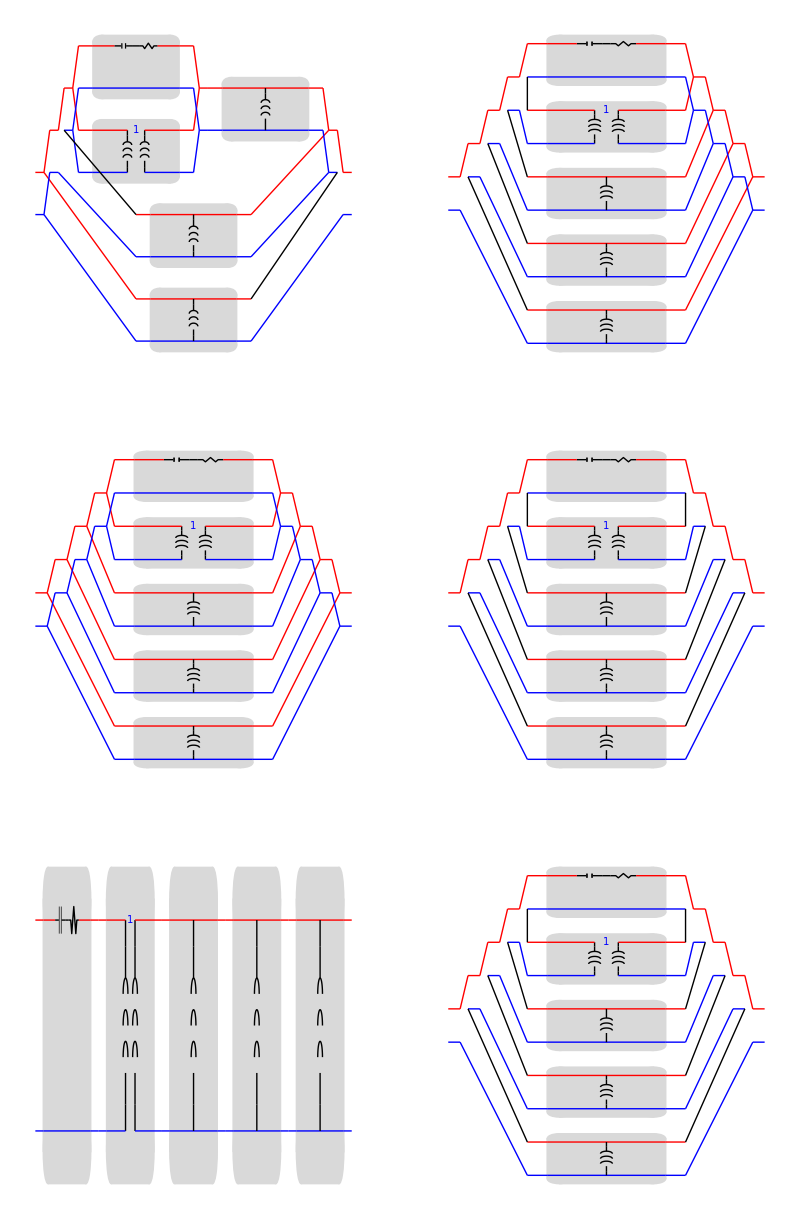

```mathematica
GraphicsGrid[Partition[CircuitGraphics[#]&/@testCircuitInterconnections,2]]
```

### Conversions among matrix representations

#### Basic test

```mathematica
Clear[k11,k12,k21,k22]

ToA[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToB[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToZ[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToY[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToH[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToP[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
ToS[#[{k11,k12},{k21,k22}]]&/@CompleteTwoportMatrices
```

{^A{{k11,k12},{k21,k22}},^A{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^A{{k11/k21,k12-(k11 k22)/k21},{1/k21,-k22/k21}},^A{{-k22/k21,1/k21},{k12-(k11 k22)/k21,k11/k21}},^A{{k12-(k11 k22)/k21,k11/k21},{-k22/k21,1/k21}},^A{{1/k21,-k22/k21},{k11/k21,k12-(k11 k22)/k21}},^A{{(k12 k21+(1+k11) (1-k22))/(2 k21),(25 (-k12 k21+(1+k11) (1+k22)))/k21},{(-k12 k21+(1-k11) (1-k22))/(100 k21),(k12 k21+(1-k11) (1+k22))/(2 k21)}},^A{{-((-k12 k21+k11 k22) ((k12 k21)/(-k12 k21+k11 k22)^2+(1-k11/(-k12 k21+k11 k22)) (1+k22/(-k12 k21+k11 k22))))/(2 k21),-(25 (-k12 k21+k11 k22) (-(k12 k21)/(-k12 k21+k11 k22)^2+(1+k11/(-k12 k21+k11 k22)) (1+k22/(-k12 k21+k11 k22))))/k21},{-((-k12 k21+k11 k22) (-(k12 k21)/(-k12 k21+k11 k22)^2+(1-k11/(-k12 k21+k11 k22)) (1-k22/(-k12 k21+k11 k22))))/(100 k21),-((-k12 k21+k11 k22) ((k12 k21)/(-k12 k21+k11 k22)^2+(1+k11/(-k12 k21+k11 k22)) (1-k22/(-k12 k21+k11 k22))))/(2 k21)}}}

{^B{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^B{{k11,k12},{k21,k22}},^B{{k22/k12,k21-(k11 k22)/k12},{1/k12,-k11/k12}},^B{{-k11/k12,1/k12},{k21-(k11 k22)/k12,k22/k12}},^B{{1/k12,-k11/k12},{k22/k12,k21-(k11 k22)/k12}},^B{{k21-(k11 k22)/k12,k22/k12},{-k11/k12,1/k12}},^B{{(1+k12 k21+k22-k11 (1+k22))/(2 k12),-(25 (1+k11-k12 k21+k22+k11 k22))/k12},{(-1+k11+k12 k21+k22-k11 k22)/(100 k12),(1+k11+k12 k21-k22-k11 k22)/(2 k12)}},^B{{(1+k12 k21+k22-k11 (1+k22))/(2 k12),(25 (1+k11-k12 k21+k22+k11 k22))/k12},{-(-1+k11+k12 k21+k22-k11 k22)/(100 k12),(1+k11+k12 k21-k22-k11 k22)/(2 k12)}}}

{^Z{{k11/k21,k12-(k11 k22)/k21},{1/k21,-k22/k21}},^Z{{-k22/k21,1/k21},{k12-(k11 k22)/k21,k11/k21}},^Z{{k11,k12},{k21,k22}},^Z{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^Z{{k11-(k12 k21)/k22,k12/k22},{-k21/k22,1/k22}},^Z{{1/k11,-k12/k11},{k21/k11,-(k12 k21)/k11+k22}},^Z{{-(50 (1+k11+k12 k21-k22-k11 k22))/(-1+k11+k12 k21+k22-k11 k22),(100 k12)/(-1+k11+k12 k21+k22-k11 k22)},{-(100 k21)/(-1+k11+k12 k21+k22-k11 k22),(50 (1+k12 k21+k22-k11 (1+k22)))/(-1+k11+k12 k21+k22-k11 k22)}},^Z{{(50 (1+k11+k12 k21-k22-k11 k22))/(-1+k11+k12 k21+k22-k11 k22),-(100 k12)/(-1+k11+k12 k21+k22-k11 k22)},{(100 k21)/(-1+k11+k12 k21+k22-k11 k22),-(50 (1+k12 k21+k22-k11 (1+k22)))/(-1+k11+k12 k21+k22-k11 k22)}}}

{^Y{{k22/k12,k21-(k11 k22)/k12},{1/k12,-k11/k12}},^Y{{-k11/k12,1/k12},{k21-(k11 k22)/k12,k22/k12}},^Y{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^Y{{k11,k12},{k21,k22}},^Y{{1/k11,-k12/k11},{k21/k11,-(k12 k21)/k11+k22}},^Y{{k11-(k12 k21)/k22,k12/k22},{-k21/k22,1/k22}},^Y{{(1+k12 k21+k22-k11 (1+k22))/(50 (1+k11-k12 k21+k22+k11 k22)),-k12/(25 (1+k11-k12 k21+k22+k11 k22))},{k21/(25 (1+k11-k12 k21+k22+k11 k22)),(-1-k12 k21+k11 (-1+k22)+k22)/(50 (1+k11-k12 k21+k22+k11 k22))}},^Y{{(-1+k11-k12 k21-k22+k11 k22)/(50 (1+k11-k12 k21+k22+k11 k22)),k12/(25 (1+k11-k12 k21+k22+k11 k22))},{-k21/(25 (1+k11-k12 k21+k22+k11 k22)),(1+k11+k12 k21-k22-k11 k22)/(50 (1+k11-k12 k21+k22+k11 k22))}}}

{^H{{k12/k22,k11-(k12 k21)/k22},{1/k22,-k21/k22}},^H{{-k12/k11,1/k11},{-(k12 k21)/k11+k22,k21/k11}},^H{{k11-(k12 k21)/k22,k12/k22},{-k21/k22,1/k22}},^H{{1/k11,-k12/k11},{k21/k11,-(k12 k21)/k11+k22}},^H{{k11,k12},{k21,k22}},^H{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^H{{(50 (1+k11-k12 k21+k22+k11 k22))/(1+k12 k21+k22-k11 (1+k22)),(2 k12)/(1+k12 k21+k22-k11 (1+k22))},{(2 k21)/(1+k12 k21+k22-k11 (1+k22)),-(-1+k11+k12 k21+k22-k11 k22)/(50 (-1+k11-k12 k21-k22+k11 k22))}},^H{{(50 (1+k11-k12 k21+k22+k11 k22))/(-1+k11-k12 k21-k22+k11 k22),(2 k12)/(1+k12 k21+k22-k11 (1+k22))},{(2 k21)/(1+k12 k21+k22-k11 (1+k22)),(-1+k11+k12 k21+k22-k11 k22)/(50 (-1+k11-k12 k21-k22+k11 k22))}}}

{^P{{k21/k11,-(k12 k21)/k11+k22},{1/k11,-k12/k11}},^P{{-k21/k22,1/k22},{k11-(k12 k21)/k22,k12/k22}},^P{{1/k11,-k12/k11},{k21/k11,-(k12 k21)/k11+k22}},^P{{k11-(k12 k21)/k22,k12/k22},{-k21/k22,1/k22}},^P{{k22/(-k12 k21+k11 k22),k12/(k12 k21-k11 k22)},{k21/(k12 k21-k11 k22),k11/(-k12 k21+k11 k22)}},^P{{k11,k12},{k21,k22}},^P{{(-1+k11+k12 k21+k22-k11 k22)/(50 (-1-k12 k21+k11 (-1+k22)+k22)),(2 k12)/(1+k11+k12 k21-k22-k11 k22)},{(2 k21)/(k12 k21-(1+k11) (-1+k22)),-(50 (1+k11-k12 k21+k22+k11 k22))/(k12 k21-(1+k11) (-1+k22))}},^P{{-(-1+k11+k12 k21+k22-k11 k22)/(50 (-1-k12 k21+k11 (-1+k22)+k22)),(2 k12)/(1+k11+k12 k21-k22-k11 k22)},{(2 k21)/(1+k11+k12 k21-k22-k11 k22),(50 (1+k11-k12 k21+k22+k11 k22))/(1+k11+k12 k21-k22-k11 k22)}}}

{^S{{(k11+k12/50-50 k21-k22)/(k11+k12/50+50 k21+k22),(2 (-k12 k21+k11 k22))/(k11+k12/50+50 k21+k22)},{2/(k11+k12/50+50 k21+k22),(-k11+k12/50-50 k21+k22)/(k11+k12/50+50 k21+k22)}},^S{{(k12/(50 (k12 k21-k11 k22))-(50 k21)/(k12 k21-k11 k22)-k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22))/(k12/(50 (k12 k21-k11 k22))+(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22)),(2 (-(k12 k21)/(k12 k21-k11 k22)^2+(k11 k22)/(-k12 k21+k11 k22)^2))/(k12/(50 (k12 k21-k11 k22))+(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22))},{2/(k12/(50 (k12 k21-k11 k22))+(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22)),(k12/(50 (k12 k21-k11 k22))-(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)-k22/(-k12 k21+k11 k22))/(k12/(50 (k12 k21-k11 k22))+(50 k21)/(k12 k21-k11 k22)+k11/(-k12 k21+k11 k22)+k22/(-k12 k21+k11 k22))}},^S{{(-50/k21+k11/k21+k22/k21+1/50 (k12-(k11 k22)/k21))/(50/k21+k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21)),(2 (-(k11 k22)/k21^2-(k12-(k11 k22)/k21)/k21))/(50/k21+k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21))},{2/(50/k21+k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21)),(-50/k21-k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21))/(50/k21+k11/k21-k22/k21+1/50 (k12-(k11 k22)/k21))}},^S{{(1/(50 k21)-k11/k21-k22/k21-50 (k12-(k11 k22)/k21))/(1/(50 k21)+k11/k21-k22/k21+50 (k12-(k11 k22)/k21)),(2 (-(k11 k22)/k21^2-(k12-(k11 k22)/k21)/k21))/(1/(50 k21)+k11/k21-k22/k21+50 (k12-(k11 k22)/k21))},{2/(1/(50 k21)+k11/k21-k22/k21+50 (k12-(k11 k22)/k21)),(1/(50 k21)+k11/k21+k22/k21-50 (k12-(k11 k22)/k21))/(1/(50 k21)+k11/k21-k22/k21+50 (k12-(k11 k22)/k21))}},^S{{(k12-1/k21+k11/(50 k21)+(50 k22)/k21-(k11 k22)/k21)/(k12+1/k21+k11/(50 k21)-(50 k22)/k21-(k11 k22)/k21),(2 ((k11 k22)/k21^2+(k12-(k11 k22)/k21)/k21))/(k12+1/k21+k11/(50 k21)-(50 k22)/k21-(k11 k22)/k21)},{2/(k12+1/k21+k11/(50 k21)-(50 k22)/k21-(k11 k22)/k21),(-k12+1/k21+k11/(50 k21)+(50 k22)/k21+(k11 k22)/k21)/(k12+1/k21+k11/(50 k21)-(50 k22)/k21-(k11 k22)/k21)}},^S{{(-k12+1/k21-(50 k11)/k21-k22/(50 k21)+(k11 k22)/k21)/(k12+1/k21+(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21),(2 ((k11 k22)/k21^2+(k12-(k11 k22)/k21)/k21))/(k12+1/k21+(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21)},{2/(k12+1/k21+(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21),(k12-1/k21-(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21)/(k12+1/k21+(50 k11)/k21-k22/(50 k21)-(k11 k22)/k21)}},^S{{k11,k12},{k21,k22}},^S{{k22/(-k12 k21+k11 k22),-k12/(-k12 k21+k11 k22)},{-k21/(-k12 k21+k11 k22),k11/(-k12 k21+k11 k22)}}}

#### Truth test for the normal twoports

```mathematica
Clear[m,m1,m2,k11,k12,k21,k22]

m=matrixA[{k11,k12},{k21,k22}];
{ToA[ToA[m]]===m,
ToA[ToB[m]]===m,
ToA[ToZ[m]]===m,
ToA[ToY[m]]===m,
ToA[ToH[m]]===m,
ToA[ToP[m]]===m 
}
m=matrixB[{k11,k12},{k21,k22}];
{ToB[ToA[m]]===m,
ToB[ToB[m]]===m,
ToB[ToZ[m]]===m,
ToB[ToY[m]]===m,
ToB[ToH[m]]===m,
ToB[ToP[m]]===m
}
m=matrixZ[{k11,k12},{k21,k22}];
{ToZ[ToA[m]]===m,
ToZ[ToB[m]]===m,
ToZ[ToZ[m]]===m,
ToZ[ToY[m]]===m,
ToZ[ToH[m]]===m,
ToZ[ToP[m]]===m
}
m=matrixY[{k11,k12},{k21,k22}];
{ToY[ToA[m]]===m,
ToY[ToB[m]]===m,
ToY[ToZ[m]]===m,
ToY[ToY[m]]===m,
ToY[ToH[m]]===m,
ToY[ToP[m]]===m
}
m=matrixH[{k11,k12},{k21,k22}];
{ToH[ToA[m]]===m,
ToH[ToB[m]]===m,
ToH[ToZ[m]]===m,
ToH[ToY[m]]===m,
ToH[ToH[m]]===m,
ToH[ToP[m]]===m
}
m=matrixP[{k11,k12},{k21,k22}];
{ToP[ToA[m]]===m,
ToP[ToB[m]]===m,
ToP[ToZ[m]]===m,
ToP[ToY[m]]===m,
ToP[ToH[m]]===m,
ToP[ToP[m]]===m
}
```

{True,True,True,True,True,True}

{True,True,True,True,True,True}

{True,True,True,True,True,True}

«3 more identical outputs»

#### Truth test for the S and T matrices

I have had to add some tricks to get by the symbolic processing.

```mathematica
Clear[m,m1,m2,k11,k12,k21,k22]

m=matrixA[{k11,k12},{k21,k22}];
m1=(ToA[ToS[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
m2=(ToA[ToT[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
{m1===(m/.{k11->1,k12->π,k21->E,k22->E ^π}),
m2===(m/.{k11->1,k12->π,k21->E,k22->E ^π})
}
m=matrixB[{k11,k12},{k21,k22}];
{ToB[ToS[m]]===m,
ToB[ToT[m]]===m
}
m=matrixZ[{k11,k12},{k21,k22}];
{ToZ[ToS[m]]===m,
ToZ[ToT[m]]===m
}
m=matrixY[{k11,k12},{k21,k22}];
{ToY[ToS[m]]===m,
ToY[ToT[m]]===m
}
m=matrixH[{k11,k12},{k21,k22}];
{ToH[ToS[m]]===m,
ToH[ToT[m]]===m
}
m=matrixP[{k11,k12},{k21,k22}];
{ToP[ToS[m]]===m,
ToP[ToT[m]]===m
}
m=matrixS[{k11,k12},{k21,k22}];
m1=(ToS[ToS[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
m2=(ToS[ToT[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
{m1===(m/.{k11->1,k12->π,k21->E,k22->E ^π}),
m2===(m/.{k11->1,k12->π,k21->E,k22->E ^π})
}
m=matrixT[{k11,k12},{k21,k22}];
m1=(ToT[ToS[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
m2=(ToT[ToT[m]])/.{k11->1,k12->π,k21->E,k22->E ^π}//Simplify;
{m1===(m/.{k11->1,k12->π,k21->E,k22->E ^π}),
m2===(m/.{k11->1,k12->π,k21->E,k22->E ^π})
}
```

{True,True}

{True,True}

{True,True}

«5 more identical outputs»

### The twoport matrices

```mathematica
Clear[z,z1,z2,z3,r1,r2,α,β,γ,l,n,m,rbe,b,yce,ygs,gm,yds]
TwoportSeriesABCD[z]
TwoportSeriesDownABCD[z]
TwoportShuntABCD[z]
TwoportLeftRightABCD[z1,z2]
TwoportGyratorABCD[α]
TwoportInvertABCD[]
TwoportWaveguideABCD[z0,β,l]
TwoportLossyWaveguideABCD[z0,γ,l]
TwoportTransformerABCD[n]
TwoportPiABCD[z1,z2,z3]
TwoportTeeABCD[z1,z2,z3]
TwoportGammaIABCD[z1,z2]
TwoportGammaIIABCD[z1,z2]
TwoportUnbalancedLadderABCD[z1,z2,n]
TwoportCoupledInductorsABCD[z1,z2,n]
TwoportCsectionABCD[z1,z2]
TwoportHsectionABCD[z1,z2]
TwoportBoxsectionABCD[z1,z2]
TwoportXsectionABCD[z1,z2]
TwoportBalancedLadderABCD[z1,z2,n]
TwoportXsectionTeeABCD[z]
TwoportXsectionPiABCD[z1,z2]
TwoportBridgeABCD[z1,z2,r1,r2]

TwoportNPNceABCD[rbe,b,yce]
TwoportNPNcbABCD[rbe,b,yce]
TwoportNPNccABCD[rbe,b,yce]

TwoportNMOScsABCD[ygs,gm,yds]
TwoportNMOScgABCD[ygs,gm,yds]
TwoportNMOScdABCD[ygs,gm,yds]
```

^A{{1,z},{0,1}}

^A{{1,-z},{0,1}}

^A{{1,0},{1/z,1}}

^A{{z1,0},{0,z2}}

^A{{0,α},{-1/α,0}}

^A{{0,1},{1,0}}

^A{{Cos[l β],ⅈ z0 Sin[l β]},{(ⅈ Sin[l β])/z0,Cos[l β]}}

^A{{Cosh[l γ],ⅈ z0 Sinh[l γ]},{(ⅈ Sinh[l γ])/z0,Cosh[l γ]}}

^A{{n,0},{0,1/n}}

^A{{1+z2/z3,z2},{1/z1+(1+z2/z1)/z3,1+z2/z1}}

^A{{1+z1/z2,z1+(1+z1/z2) z3},{1/z2,1+z3/z2}}

^A{{1,z2},{1/z1,1+z2/z1}}

^A{{1+z1/z2,z1},{1/z2,1}}

^A{{(1+z1/(2 z2)) (-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))+z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2))))+1/z2((1+z1/(2 z2)) ((2^-n (-√z2+√(4 z1+z2)) (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√(4 z1+z2))+(2^-n (√z2+√(4 z1+z2)) (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√(4 z1+z2)))+z1 ((2^-n z1 (-√z2+√(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 (√z2+√(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2))))+2 z1 ((1+z1/(2 z2)) (-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))+z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))))),(1+z1/(2 z2)) ((2^-n (-√z2+√(4 z1+z2)) (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√(4 z1+z2))+(2^-n (√z2+√(4 z1+z2)) (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√(4 z1+z2)))+z1 ((2^-n z1 (-√z2+√(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 (√z2+√(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2))))+2 z1 ((1+z1/(2 z2)) (-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))+z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))))},{-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+(-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))/(2 z2)+1/z2((2^-n z1 (-√z2+√(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 (√z2+√(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+1/(2 z2)((2^-n (-√z2+√(4 z1+z2)) (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√(4 z1+z2))+(2^-n (√z2+√(4 z1+z2)) (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√(4 z1+z2)))+2 z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+(-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))/(2 z2))),(2^-n z1 (-√z2+√(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 (√z2+√(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+1/(2 z2)((2^-n (-√z2+√(4 z1+z2)) (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√(4 z1+z2))+(2^-n (√z2+√(4 z1+z2)) (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√(4 z1+z2)))+2 z1 (-(2^-n z1 ((2 z1+z2-√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2-√z2 √(4 z1+z2)))+(2^-n z1 ((2 z1+z2+√z2 √(4 z1+z2))/z1)^n)/(√z2 √(4 z1+z2) (2 z1+z2+√z2 √(4 z1+z2)))+(-(2^-n (-z2-√z2 √(4 z1+z2)) ((2 z1+z2-√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2))+(2^-n (-z2+√z2 √(4 z1+z2)) ((2 z1+z2+√z2 √(4 z1+z2))/z1)^(-1+n))/(√z2 √(4 z1+z2)))/(2 z2))}}

^A{{1+(-n+z1)/n,-n+z1+(1+(-n+z1)/n) (-n+z2)},{1/n,1+(-n+z2)/n}}

^A{{1+z1/(2 z2),z1/2},{1/z2,1}}

^A{{1+z1/(2 z2),z1/2+1/2 z1 (1+z1/(2 z2))},{1/z2,1+z1/(2 z2)}}

^A{{1+z1/(2 z2),z1/2},{1/z2+(1+z1/(2 z2))/z2,1+z1/(2 z2)}}

^A{{(z1+z2)/(z1-z2),(2 z1 z2)/(z1-z2)},{2/(z1-z2),(z1+z2)/(z1-z2)}}

^A{{1,0},{0,1}}

^A{{1,0},{0,1}}

^A{{1,0},{0,1}}

^A{{((r1+r2) (z1+z2))/(-r2 z1+r1 z2),(r2 (r1+z1) z2+r1 z1 (r2+z2))/(-r2 z1+r1 z2)},{(r1+r2+z1+z2)/(-r2 z1+r1 z2),((r1+z1) (r2+z2))/(-r2 z1+r1 z2)}}

^A{{-(rbe yce)/b,rbe/b},{-yce/b,1/b}}

^A{{(rbe yce)/(-b+rbe yce),rbe/(b-rbe yce)},{(yce+2 b yce)/(-b+rbe yce),(1+b+rbe yce)/(b-rbe yce)}}

^A{{(1+b-rbe yce)/(1+b),rbe/(1+b)},{-yce/(1+b),1/(1+b)}}

^A{{-yds/gm,1/gm},{-(yds ygs)/gm,ygs/gm}}

^A{{yds/(gm+yds),-1/(gm+yds)},{(yds ygs)/(gm+yds),-(gm+yds+ygs)/(gm+yds)}}

^A{{(gm+yds+ygs)/(gm+ygs),-1/(gm+ygs)},{(yds ygs)/(gm+ygs),-ygs/(gm+ygs)}}

### The general documentation

The general usage:

```mathematica
?Twoport
```

#### The two-ports

```mathematica
?Twoport*ABCD
```

#### Two-port matrix formats

```mathematica
?matrix*
```

#### Converting two-ports

```mathematica
?ToA
```

#### Interconnecting two-ports

```mathematica
?CircuitParallel
```

#### Circuit operations

```mathematica
?CircuitGraphics
```

```mathematica
?CircuitExpression
```

#### Plotting operations

```mathematica
?LogLinearPlotSparameters
```

```mathematica
?SmithPlot
```

### Plotting

#### Smithplot

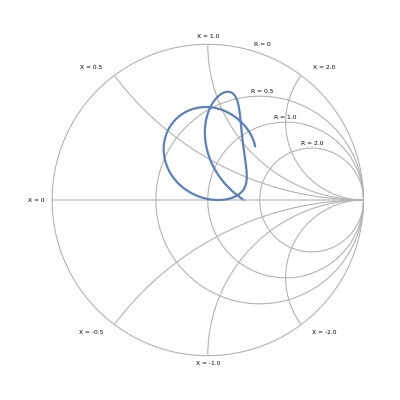

```mathematica
SmithPlot[{50+30ⅈ+30(Cos[ω^1.1]+ⅈ Sin[ω 1.1])},{ω,1,10}]
```

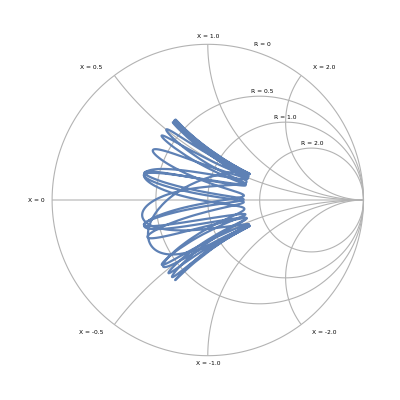

```mathematica
SmithPlot[{50+30(Cos[ω^2.1]+ⅈ Sin[ω 2.1])},{ω,1,10}]
```

## The circuit demonstration examples

### Basic usage example

We will construct a simple resonant circuit. We start by cascading two two-ports, a resistor onject in parallel with capacitor object as a series two-port, and a shunt inductor two-port. Note that we specify the primitives as objects, so that their impedances will be correctly computed. At this point all component values are symbols:

```mathematica
BasicCircuitParameters={c1->10. 10^-12,l1->.2 10^-6,r1->.1};BasicCircuit=CircuitCascade[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]] ,TwoportShunt[OneportL[l1]]]
```

CircuitCascade[TwoportSeries[OneportSeries[OneportC[c1],OneportR[r1]]],TwoportShunt[OneportL[l1]]]

We now check whether the circuit is arranged the way we intended by plotting it.

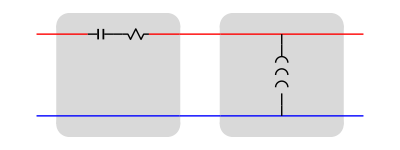

```mathematica
CircuitGraphics[BasicCircuit]
```

Our next step is to compute the ABCD matrix of the circuit. This is achieved by a simple conversion, for which we specify the frequency parameter.

```mathematica
(BasicCircuitExpression=CircuitExpression[BasicCircuit,ω])
```

^A{{1-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω),r1-ⅈ/(c1 ω)},{-ⅈ/(l1 ω),1}}

We can obtain this object as a pretty printed matrix by using Mathematica’s built-in function:

```mathematica
(BasicCircuitExpression)//MatrixForm
```

(1-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω) | r1-ⅈ/(c1 ω)
-ⅈ/(l1 ω) | 1)

Next, we compute the circuit’s s-parameters. We have to choose input and output impedances. We use a very high impedance at the right end of the circuit, and a 50 Ω resistor for the cable.

```mathematica
BasicCircuitExpressionSparam=ToS[BasicCircuitExpression,{50.,1. 10^7}]//Chop
```

^S{{(1/50 (r1-ⅈ/(c1 ω))+(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω))/(2+1/50 (r1-ⅈ/(c1 ω))-(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω)),0.00447214/(2+1/50 (r1-ⅈ/(c1 ω))-(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω))},{894.427/(2+1/50 (r1-ⅈ/(c1 ω))-(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω)),(1/50 (r1-ⅈ/(c1 ω))+(50 ⅈ)/(l1 ω)+(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω))/(2+1/50 (r1-ⅈ/(c1 ω))-(50 ⅈ)/(l1 ω)-(ⅈ (r1-ⅈ/(c1 ω)))/(l1 ω))}}

We pick out s_11 and plot its amplitude over a range of frequencies. We also remember to insert numerical values for the circuit parameters. We  plot the argument of  s_11, which gives us the phase.

```mathematica
BasicCircuitExpressionSparam/.BasicCircuitParameters
```

^S{{(1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)+(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω),0.00447214/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)},{894.427/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω),(1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)+(0.+2.5×10^8 ⅈ)/ω+((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)}}

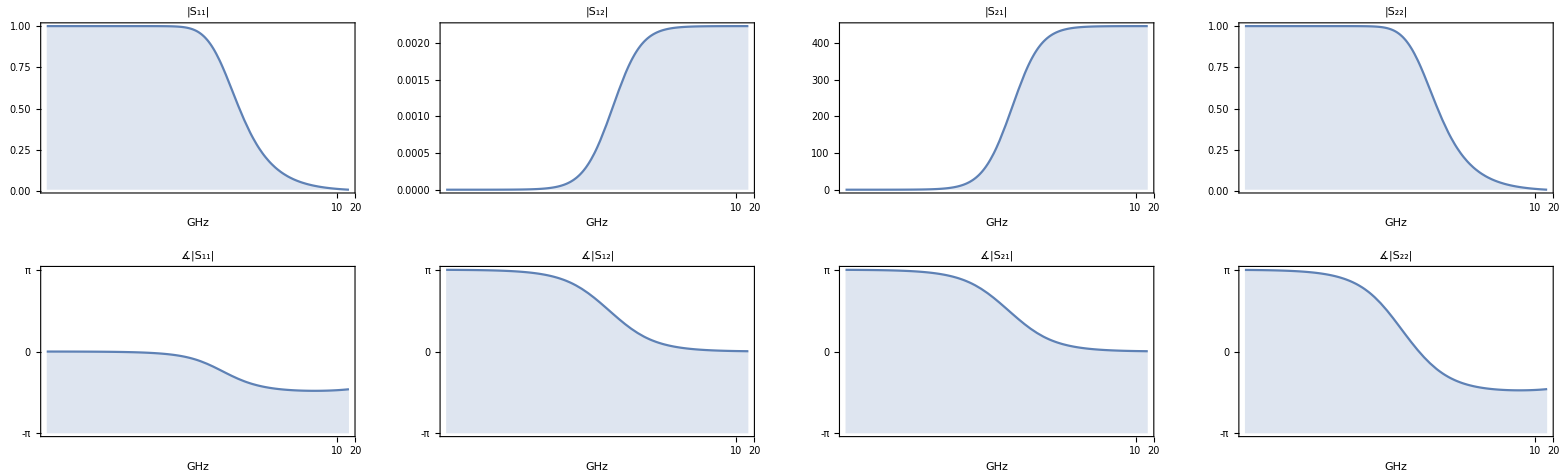

```mathematica
LogLinearPlotSparameters[BasicCircuitExpressionSparam/.BasicCircuitParameters,{ω, 10^6, 10^11}]
```

```mathematica
List@@(BasicCircuitExpressionSparam/.BasicCircuitParameters)
```

{{(1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)+(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω),0.00447214/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)},{894.427/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω),(1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)+(0.+2.5×10^8 ⅈ)/ω+((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)/(2+1/50 (0.1-(0.+1.×10^11 ⅈ)/ω)-(0.+2.5×10^8 ⅈ)/ω-((0.+5.×10^6 ⅈ) (0.1-(0.+1.×10^11 ⅈ)/ω))/ω)}}

We can now plot these on a Smith chart.

```mathematica
impedance=List@@(Flatten[((ToZ[BasicCircuitExpression]/.BasicCircuitParameters))])
```

{{0.1-(0.+1.×10^11 ⅈ)/ω+(0.+2.×10^-7 ⅈ) ω,(0.-2.×10^-7 ⅈ) ω},{(0.+2.×10^-7 ⅈ) ω,(0.-2.×10^-7 ⅈ) ω}}

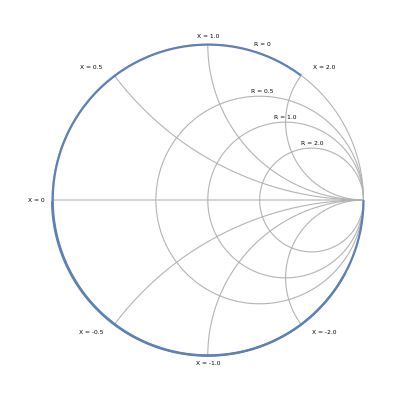
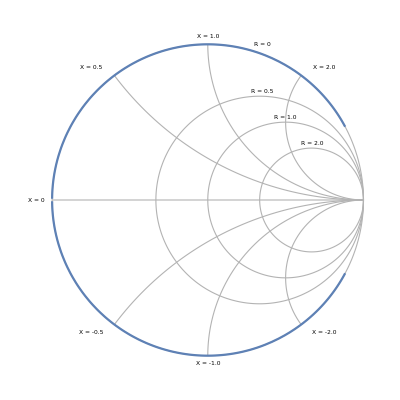

```mathematica
SmithPlot[#,{ω,10^6,10^9}]&/@impedance
```

### Highpass

CircuitCascade[TwoportSeries[OneportC[c1]],TwoportShunt[OneportL[l1]]]

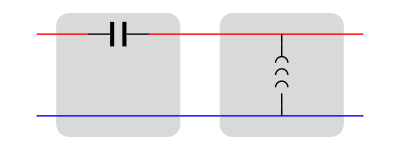

^A{{1-1/(c1 l1 ω^2),-ⅈ/(c1 ω)},{-ⅈ/(l1 ω),1}}

(1-1/(c1 l1 ω^2) | -ⅈ/(c1 ω)
-ⅈ/(l1 ω) | 1)

^S{{(-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+(50 ⅈ)/(l1 ω))/(2-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-(50 ⅈ)/(l1 ω)),0.00447214/(2-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-(50 ⅈ)/(l1 ω))},{894.427/(2-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-(50 ⅈ)/(l1 ω)),(1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)+(50 ⅈ)/(l1 ω))/(2-1/(c1 l1 ω^2)-ⅈ/(50 c1 ω)-(50 ⅈ)/(l1 ω))}}

```mathematica
HighpassCircuit=CircuitCascade[TwoportSeries[OneportC[c1]] ,TwoportShunt[OneportL[l1]]]
CircuitGraphics[HighpassCircuit]
HighpassCircuitExpression=CircuitExpression[HighpassCircuit,ω]
MatrixForm[HighpassCircuitExpression]
HighpassCircuitExpressionSparam=ToS[HighpassCircuitExpression,{50.,1. 10^7}]//Chop
HighpassCircuitParameters={c1->10. 10^-10,l1->.2 10^-6};
```

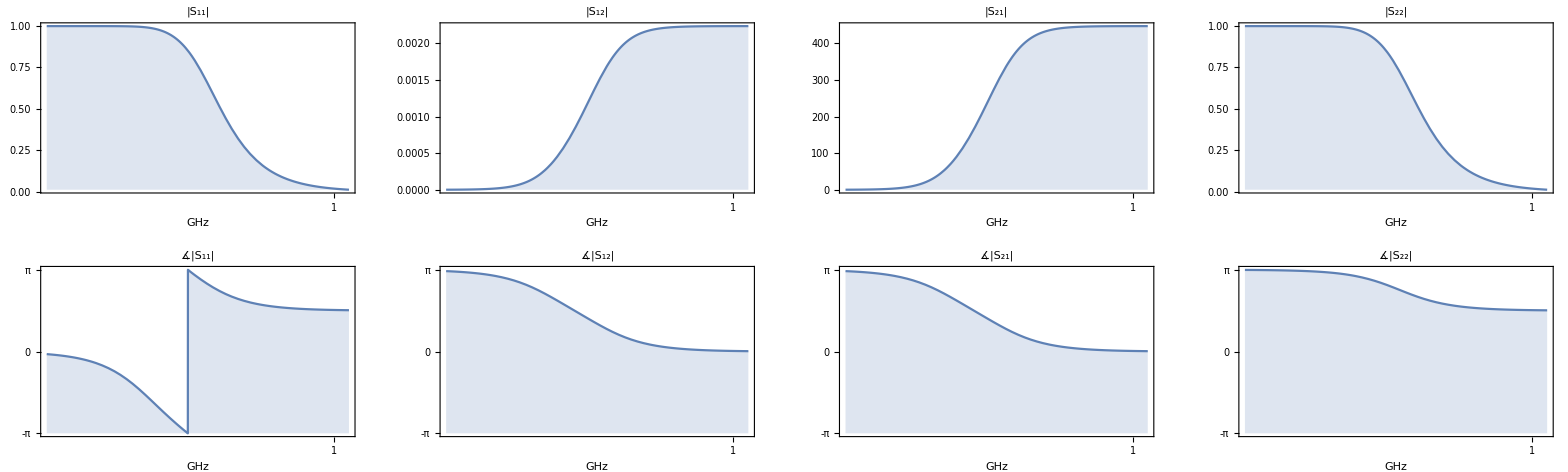

```mathematica
LogLinearPlotSparameters[HighpassCircuitExpressionSparam/.HighpassCircuitParameters,{ω,1 10^6, 10^10}]
```

### Lowpass

CircuitCascade[TwoportSeries[OneportL[l1]],TwoportShunt[OneportC[c1]]]

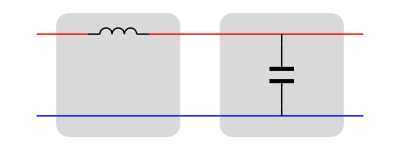

^A{{1-c1 l1 ω^2,ⅈ l1 ω},{ⅈ c1 ω,1}}

(1-c1 l1 ω^2 | ⅈ l1 ω
ⅈ c1 ω | 1)

^S{{(-50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2)/(2+50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2),0.00447214/(2+50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2)},{894.427/(2+50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2),(-50 ⅈ c1 ω+(ⅈ l1 ω)/50+c1 l1 ω^2)/(2+50 ⅈ c1 ω+(ⅈ l1 ω)/50-c1 l1 ω^2)}}

```mathematica
LowpassCircuit=CircuitCascade[TwoportSeries[OneportL[l1]] ,TwoportShunt[OneportC[c1]]]
CircuitGraphics[LowpassCircuit]
LowpassCircuitExpression=CircuitExpression[LowpassCircuit,ω]
MatrixForm[LowpassCircuitExpression]
LowpassCircuitExpressionSparam=ToS[LowpassCircuitExpression,{50.,1. 10^7}]//Chop
LowpassCircuitParameters={c1->10. 10^-10,l1->.2 10^-6};
```

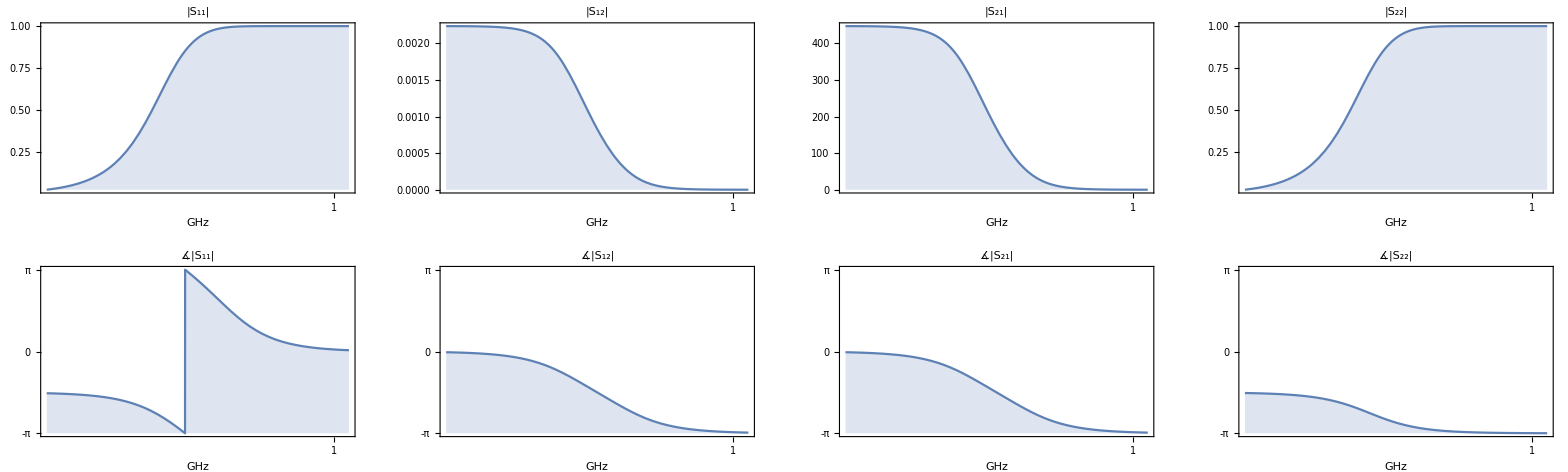

```mathematica
LogLinearPlotSparameters[LowpassCircuitExpressionSparam/.LowpassCircuitParameters,{ω,1 10^6, 10^10}]
```

### Bandpass

CircuitCascade[CircuitCascade[TwoportSeries[OneportL[l1]],TwoportSeries[OneportC[c1]]],CircuitCascade[TwoportShunt[OneportC[c1]],TwoportShunt[OneportL[l1]]]]

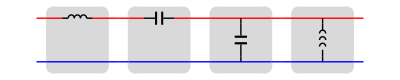

^A{{1+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω),-ⅈ/(c1 ω)+ⅈ l1 ω},{-ⅈ/(l1 ω)+ⅈ c1 ω,1}}

^S{{(-50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω))/(2+50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω)),0.00447214/(2+50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω))},{894.427/(2+50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω)),(-50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)-(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω))/(2+50 (-ⅈ/(l1 ω)+ⅈ c1 ω)+1/50 (-ⅈ/(c1 ω)+ⅈ l1 ω)+(-ⅈ/(l1 ω)+ⅈ c1 ω) (-ⅈ/(c1 ω)+ⅈ l1 ω))}}

```mathematica
BandpassCircuit=CircuitCascade[CircuitCascade[TwoportSeries[OneportL[l1]] ,TwoportSeries[OneportC[c1]]] ,CircuitCascade[TwoportShunt[OneportC[c1]],TwoportShunt[OneportL[l1]] ]]
CircuitGraphics[BandpassCircuit]
BandpassCircuitExpression=CircuitExpression[BandpassCircuit,ω]
BandpassCircuitExpressionSparam=ToS[BandpassCircuitExpression,{50.,1. 10^7}]//Chop
BandpassCircuitParameters={c1->10. 10^-10,l1->.2 10^-6};
```

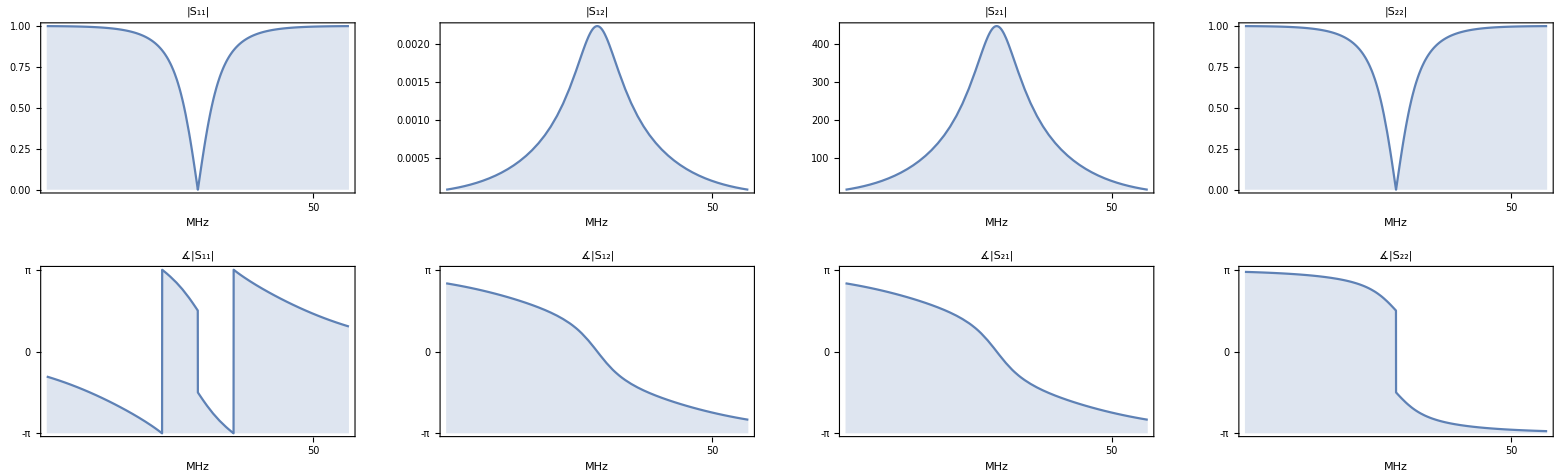

```mathematica
LogLinearPlotSparameters[BandpassCircuitExpressionSparam/.BandpassCircuitParameters,{ω, 10^7,5 10^8}]
```

### 5 Pole lowpass elliptic

From Bahl, chapter 12

CircuitCascade[TwoportSeries[OneportL[l1]],CircuitCascade[TwoportPi[OneportSeries[OneportL[l2],OneportC[c2]],OneportL[l3],OneportSeries[OneportL[l4],OneportC[c4]]],TwoportSeries[OneportL[l5]]]]

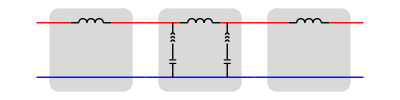

```mathematica
fivePoleLowpassCircuitParameters={c2->23 10^-12,c4->19.5 10^-12,l1->45.7 10^-9,l2->7.7 10^-9,l3->79.2 10^-9,l4->23 10^-9,l5->34.7 10^-9};
thePie=TwoportPi[OneportSeries[OneportL[l2],OneportC[c2]],OneportL[l3],OneportSeries[OneportL[l4],OneportC[c4]]];
fivePoleLowpassCircuit=CircuitCascade[TwoportSeries[OneportL[l1]],CircuitCascade[TwoportPi[OneportSeries[OneportL[l2],OneportC[c2]],OneportL[l3],OneportSeries[OneportL[l4],OneportC[c4]]],TwoportSeries[OneportL[l5]]]]
CircuitGraphics[fivePoleLowpassCircuit]
```

```mathematica
fivePoleLowpassCircuitExpression=CircuitExpression[fivePoleLowpassCircuit/.fivePoleLowpassCircuitParameters,ω]//Simplify
```

^A{{(0.+0. ⅈ)+((-2.22965×10^18+0. ⅈ)+(4.44348+0. ⅈ) ω^2)/((-2.22965×10^18+0. ⅈ)+ω^2)+((-2.44525×10^19+0. ⅈ) ω^2+(28.3593+0. ⅈ) ω^4)/((1.25898×10^37+0. ⅈ)-(7.87618×10^18+0. ⅈ) ω^2+(1.+0. ⅈ) ω^4),((0.+2.52971×10^67 ⅈ) ω-(0.+6.40235×10^49 ⅈ) ω^3+(0.+5.39826×10^31 ⅈ) ω^5-(0.+1.74794×10^13 ⅈ) ω^7+(0.+1.73321×10^-6 ⅈ) ω^9)/((1.58503×10^74+0. ⅈ)-(1.98319×10^56+0. ⅈ) ω^2+(8.72138×10^37+0. ⅈ) ω^4-(1.57524×10^19+0. ⅈ) ω^6+(1.+0. ⅈ) ω^8)},{((0.+5.35067×10^26 ⅈ) ω-(0.+6.20553×10^8 ⅈ) ω^3)/((1.25898×10^37+0. ⅈ)-(7.87618×10^18+0. ⅈ) ω^2+(1.+0. ⅈ) ω^4),((7.10887×10^55+0. ⅈ)-(2.91396×10^38+0. ⅈ) ω^2+(2.34689×10^20+0. ⅈ) ω^4-(32.8189+0. ⅈ) ω^6)/((7.10887×10^55+0. ⅈ)-(5.70629×10^37+0. ⅈ) ω^2+(1.35227×10^19+0. ⅈ) ω^4-(1.+0. ⅈ) ω^6)}}

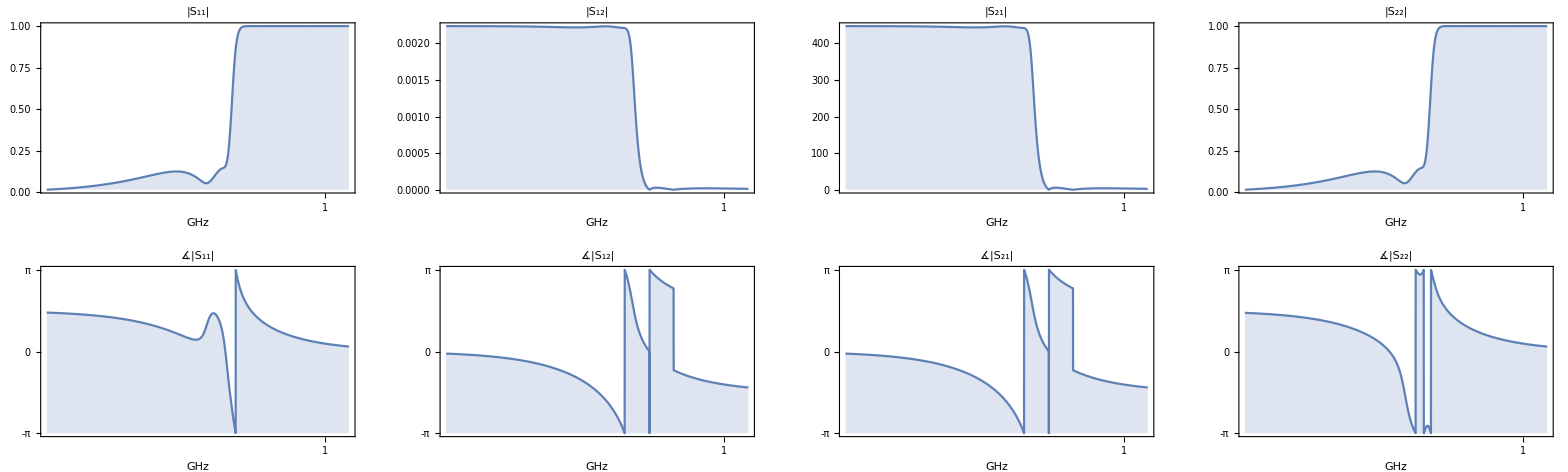

```mathematica
fivePoleLowpassCircuitExpressionSparam=ToS[fivePoleLowpassCircuitExpression,{50.,1. 10^7}];
LogLinearPlotSparameters[fivePoleLowpassCircuitExpressionSparam,{ω,3 10^7,10 10^9}]
```

### 3 Pole bandpass

From Bahl, chapter 12

CircuitCascade[TwoportPi[OneportC[c1],OneportC[c2],OneportC[c3]],CircuitCascade[TwoportSeries[OneportParallel[OneportC[c4],OneportL[l1]]],CircuitCascade[TwoportPi[OneportC[c4],OneportC[c5],OneportC[c4]],CircuitCascade[TwoportSeries[OneportParallel[OneportC[c4],OneportL[l1]]],CircuitCascade[TwoportPi[OneportC[c4],OneportC[c5],OneportC[c4]],CircuitCascade[TwoportSeries[OneportParallel[OneportC[c4],OneportL[l1]]],TwoportPi[OneportC[c1],OneportC[c2],OneportC[c3]]]]]]]]

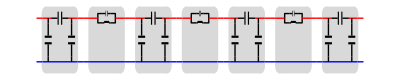

```mathematica
ThreepoleBandpassCircuitParameters={c1->0.1 10^-12,c2->.15481 10^-12,c3->.12258 10^-12,c4->.26309 10^-12,c5->.012438 10^-12,l1->10 10^-9};

firstPie=TwoportPi[OneportC[c1],OneportC[c2],OneportC[c3]];
secondPie=TwoportPi[OneportC[c4],OneportC[c5],OneportC[c4]];
serial=TwoportSeries[OneportParallel[OneportC[c4],OneportL[l1]]];

ThreepoleBandpassCircuit=CircuitCascade[firstPie,CircuitCascade[serial,CircuitCascade[secondPie,CircuitCascade[serial,CircuitCascade[secondPie,CircuitCascade[serial,firstPie]]]]]]

CircuitGraphics[ThreepoleBandpassCircuit]
```

```mathematica
ThreepoleBandpassCircuitExpression=CircuitExpression[ThreepoleBandpassCircuit/.ThreepoleBandpassCircuitParameters,ω]
```

^A{{-1/ω(0.+6.45953×10^12 ⅈ) ((0.+0. ⅈ)+(0.+3.89849×10^-10 ⅈ) ω+((4.07168×10^-23+0. ⅈ) ω^3)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)+((0.-3.89547×10^6 ⅈ) ω+(0.+3.52884×10^-14 ⅈ) ω^3-(0.+7.7073×10^-35 ⅈ) ω^5)/(((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2))+(1.79181+0. ⅈ) (((-2.83162×10^19+0. ⅈ)+(0.217565+0. ⅈ) ω^2-(4.17113×10^-22+0. ⅈ) ω^4)/(((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2)+(ω ((0.+0. ⅈ)+(0.+3.89849×10^-10 ⅈ) ω+((4.07168×10^-23+0. ⅈ) ω^3)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)+((0.-3.89547×10^6 ⅈ) ω+(0.+3.52884×10^-14 ⅈ) ω^3-(0.+7.7073×10^-35 ⅈ) ω^5)/(((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2)))/((0.-1.×10^8 ⅈ)+(0.+2.6309×10^-13 ⅈ) ω^2)),-(((0.+6.45953×10^12 ⅈ) ((0.+3.35692×10^27 ⅈ)-(0.+3.55544×10^7 ⅈ) ω^2+(0.+1.23481×10^-13 ⅈ) ω^4-(0.+1.39901×10^-34 ⅈ) ω^6))/(ω ((0.+1.×10^24 ⅈ)-(0.+7892.7 ⅈ) ω^2+(0.+2.07649×10^-17 ⅈ) ω^4-(0.+1.82101×10^-38 ⅈ) ω^6)))+((1.79181+0. ⅈ) ((0.-1.2196×10^48 ⅈ)+(0.+1.94846×10^28 ⅈ) ω^2-(0.+1.14416×10^8 ⅈ) ω^4+(0.+2.92383×10^-13 ⅈ) ω^6-(0.+2.7367×10^-34 ⅈ) ω^8))/((1.×10^32+0. ⅈ) ω-(1.05236×10^12+0. ⅈ) ω^3+(4.15298×10^-9+0. ⅈ) ω^5-(7.28405×10^-30+0. ⅈ) ω^7+(4.7909×10^-51+0. ⅈ) ω^9)},{(1.64595+0. ⅈ) ((0.+0. ⅈ)+(0.+3.89849×10^-10 ⅈ) ω+((4.07168×10^-23+0. ⅈ) ω^3)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)+((0.-3.89547×10^6 ⅈ) ω+(0.+3.52884×10^-14 ⅈ) ω^3-(0.+7.7073×10^-35 ⅈ) ω^5)/(((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2))+(0.+3.01761×10^-13 ⅈ) ω (((-2.83162×10^19+0. ⅈ)+(0.217565+0. ⅈ) ω^2-(4.17113×10^-22+0. ⅈ) ω^4)/(((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2)+(ω ((0.+0. ⅈ)+(0.+3.89849×10^-10 ⅈ) ω+((4.07168×10^-23+0. ⅈ) ω^3)/((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)+((0.-3.89547×10^6 ⅈ) ω+(0.+3.52884×10^-14 ⅈ) ω^3-(0.+7.7073×10^-35 ⅈ) ω^5)/(((0.+1.×10^8 ⅈ)-(0.+2.6309×10^-13 ⅈ) ω^2)^2)))/((0.-1.×10^8 ⅈ)+(0.+2.6309×10^-13 ⅈ) ω^2)),((1.64595+0. ⅈ) ((0.+3.35692×10^27 ⅈ)-(0.+3.55544×10^7 ⅈ) ω^2+(0.+1.23481×10^-13 ⅈ) ω^4-(0.+1.39901×10^-34 ⅈ) ω^6))/((0.+1.×10^24 ⅈ)-(0.+7892.7 ⅈ) ω^2+(0.+2.07649×10^-17 ⅈ) ω^4-(0.+1.82101×10^-38 ⅈ) ω^6)+((0.+3.01761×10^-13 ⅈ) ω ((0.-1.2196×10^48 ⅈ)+(0.+1.94846×10^28 ⅈ) ω^2-(0.+1.14416×10^8 ⅈ) ω^4+(0.+2.92383×10^-13 ⅈ) ω^6-(0.+2.7367×10^-34 ⅈ) ω^8))/((1.×10^32+0. ⅈ) ω-(1.05236×10^12+0. ⅈ) ω^3+(4.15298×10^-9+0. ⅈ) ω^5-(7.28405×10^-30+0. ⅈ) ω^7+(4.7909×10^-51+0. ⅈ) ω^9)}}

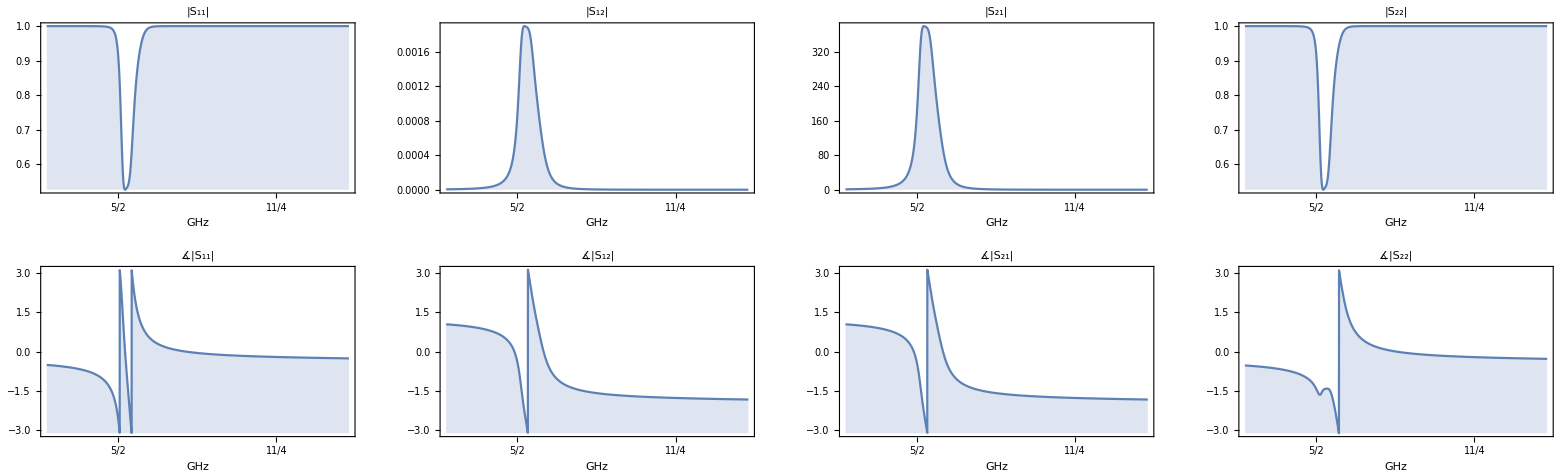

```mathematica
ThreepoleBandpassCircuitExpressionSparam=ToS[ThreepoleBandpassCircuitExpression,{50.,1. 10^7}];
PlotSparameters[ThreepoleBandpassCircuitExpressionSparam,{ω,1.5 10^10,1.8 10^10}]
```